```mathematica
(*EPD 6---------Problema 3: El intervalo [-2,2] tiene amplitud 4
Para 4 puntos, estamos hablando que el intervalo se divide entre 3*)
x0=-2
x1=-2+4/3
x2=-2+2*4/3
x3=-2+3*4/3
f[x_]:=2/(3+5x^2)
```

-2

-2/3

2/3

2

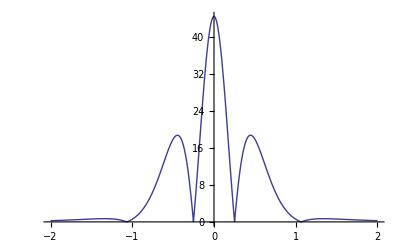

```mathematica
(*La fórmula es (|f^(4))|)/(4!)|x-x0||x-x1||x-x2||x-x3|. Por tanto primero corres ponde a estudiar la derivada en dicho intervalo:*)
Plot[Abs[f''''[x]],{x,-2,2}]
```

```mathematica
f'''''[x]
```

-(24000000 x^5)/((3+5 x^2)^6)+(4800000 x^3)/((3+5 x^2)^5)-(180000 x)/((3+5 x^2)^4)

```mathematica
Solve[%==0]
```

{{x→0},{x→-3/(√5)},{x→-1/(√5)},{x→1/(√5)},{x→3/(√5)}}

```mathematica
(*La derivada cuarta tiene el máximo en un punto intermedio del intervalo. Calculamos la derivada 5 y comprobamos que el punto crítico buscado es x=0 tal y como vemos en la gráfica:*)
Abs[f''''[0]]/4!Abs[(x-x0)(x-x1)(x-x2)(x-x3)]
```

50/27 Abs[(-2+x) (-2/3+x) (2/3+x) (2+x)]

```mathematica
(*Esta es la expresión del error para 4 puntos

Para 5 puntos el soporte se obtiene con 4 intervalos y por tanto el soporte es*)
x0=-2
x1=-1
x2=0
x3=1
x4=2
```

-2

-1

0

1

2

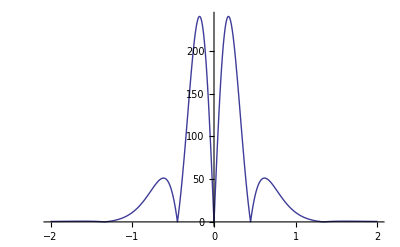

```mathematica
(*La fórmula del error absoluto es (|f^(5))|)/(5!)|x-x0||x-x1||x-x2||x-x3||x-x4|. Por tanto primero corres ponde a estudiar la derivada en dicho intervalo:*)
Plot[Abs[f'''''[x]],{x,-2,2},PlotRange->Full]
```

```mathematica
(*La derivada quinta tiene dos máximo en la zona media. Vamos a ver los puntos críticos:*)
f''''''[x]
```

(1440000000 x^6)/((3+5 x^2)^7)-(360000000 x^4)/((3+5 x^2)^6)+(21600000 x^2)/((3+5 x^2)^5)-180000/((3+5 x^2)^4)

```mathematica
NSolve[%==0]
```

{{x→-1.60847},{x→1.60847},{x→0.61772},{x→-0.61772},{x→-0.176797},{x→0.176797}}

```mathematica
(*El máximo es el más cercano al x=0, por lo que el error lo estimaremos como:*)
Abs[f'''''[0.17679663503871393]]/4!Abs[(x-x0)(x-x1)(x-x2)(x-x3)(x-x4)]
```

10.0071 Abs[(-2+x) (-1+x) x (1+x) (2+x)]

```mathematica
(*Esta es la expresión del error para 5 puntos que corresponde a P4. Por tanto, el apartado siguiente me pide sustituir x=1.2 en esa expresión:*)
%/.{x->1.2}
```

13.5264

-2

-2/3

2/3

2

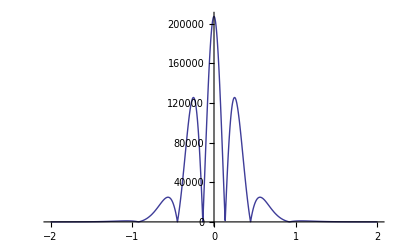

```mathematica
(*Veamos ahora el error absoluto cometido con Hermite para cuatro puntos: (|f^(8))|)/(8!)|x-x0|^2|x-x1|^2|x-x2|^2|x-x3|^2*)
x0=-2
x1=-2+4/3
x2=-2+2*4/3
x3=-2+3*4/3
Plot[Abs[f''''''''[x]],{x,-2,2},PlotRange->Full]
```

```mathematica
(*La derivada octava parece tener un máximo en la zona media. Vamos a ver los puntos críticos:*)
```

```mathematica
Solve[f'''''''''[x]==0]
```

{{x→0},{x→-√(3/5+6/(5 √5))},{x→√(3/5+6/(5 √5))},{x→-√(3/5 (5-2 √5))},{x→√(3/5 (5-2 √5))},{x→-1/5 √(3 (5-2 √5))},{x→1/5 √(3 (5-2 √5))},{x→-√(3/5 (5+2 √5))},{x→√(3/5 (5+2 √5))}}

```mathematica
(*Es en el x=0. Luego la expresión del error será:*)
Abs[f''''''''[0]]/8!(x-x0)^2(x-x1)^2(x-x2)^2(x-x3)^2
```

1250/243 (-2+x)^2 (-2/3+x)^2 (2/3+x)^2 (2+x)^2

-2

-1

0

1

2

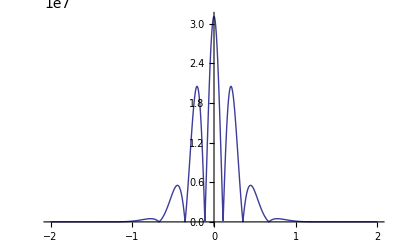

```mathematica
(*Para 5 puntosahora el error absoluto cometido con Hermite para cuatro puntos: (|f^(10))|)/(10!)|x-x0|^2|x-x1|^2|x-x2|^2|x-x3|^2|x-x4|^2*)
x0=-2
x1=-1
x2=0
x3=1
x4=2
Plot[Abs[f''''''''''[x]],{x,-2,2},PlotRange->Full]
```

```mathematica
(*Veamos que el máximo es otra vez x=0. En efecto:*)
Solve[f'''''''''''[x]==0]
```

{{x→0},{x→-√(3/5)},{x→√(3/5)},{x→-3/(√5)},{x→-1/(√5)},{x→1/(√5)},{x→3/(√5)},{x→-√(3/5 (7-4 √3))},{x→√(3/5 (7-4 √3))},{x→-√(21/5+(12 √3)/5)},{x→√(21/5+(12 √3)/5)}}

```mathematica
(*El error absoluto se expresa como:*)
Abs[f''''''''''[0]]/10!(x-x0)^2(x-x1)^2(x-x2)^2(x-x3)^2(x-x4)^2
```

6250/729 (-2+x)^2 (-1+x)^2 x^2 (1+x)^2 (2+x)^2

```mathematica
(*Pasamos al cálculo del polinomio interpolador por 3 puntos equiespaciados y por Newton*)
x0=-2
x1=0
x2=2
```

-2

0

2

```mathematica
(*Diferencias orden 0:*)
dif0=f[x0]
dif1=f[x1]
dif2=f[x2]
```

2/23

2/3

2/23

```mathematica
(*Diferencias de orden 1:*)
dif01=(dif1-dif0)/(x1-x0)
dif12=(dif2-dif1)/(x2-x1)
```

20/69

-20/69

```mathematica
(*Diferencia de orden 2:*)
dif012=(dif12-dif01)/(x2-x0)
```

-10/69

```mathematica
(*El polinomio es:*)
dif0+dif01(x-x0)+dif012(x-x0)(x-x1)
```

2/23+(20 (2+x))/69-10/69 x (2+x)

```mathematica
Expand[%]
```

2/3-(10 x^2)/69

```mathematica
(*Vamos a la interpolacion de Hermite:*)
z0=x0
z1=x0
z2=x1
z3=x1
z4=x2
z5=x2
```

-2

-2

0

0

2

2

```mathematica
(*ORDEN 0*)
dif0=f[z0]
dif1=f[z1]
dif2=f[z2]
dif3=f[z3]
dif4=f[z4]
dif5=f[z5]
```

2/23

2/23

2/3

2/3

2/23

2/23

```mathematica
(*ORDEN 1*)
dif01=f'[z0]
dif12=(dif2-dif1)/(z2-z1)
dif23=f'[z2]
dif34=(dif4-dif3)/(z4-z3)
dif45=f'[z4]
```

40/529

20/69

0

-20/69

-40/529

```mathematica
(*ORDEN 2*)
dif012=(dif12-dif01)/(z2-z0)
dif123=(dif23-dif12)/(z3-z1)
dif234=(dif34-dif23)/(z4-z2)
dif345=(dif45-dif34)/(z5-z3)
```

170/1587

-10/69

-10/69

170/1587

```mathematica
(*ORDEN 3*)
dif0123=(dif123-dif012)/(z3-z0)
dif1234=(dif234-dif123)/(z4-z1)
dif2345=(dif345-dif234)/(z5-z2)
```

-200/1587

0

200/1587

```mathematica
(*ORDEN 4*)
dif01234=(dif1234-dif0123)/(z4-z0)
dif12345=(dif2345-dif1234)/(z5-z1)
```

50/1587

50/1587

```mathematica
(*ORDEN 5*)
dif012345=(dif12345-dif01234)/(z5-z0)
```

0

```mathematica
(*El polinomio de Hermite es:*)
dif0+dif01(x-z0)+dif012(x-z0)(x-z1)+dif0123(x-z0)(x-z1)(x-z2)+dif01234(x-z0)(x-z1)(x-z2)(x-z3)+dif012345(x-z0)(x-z1)(x-z2)(x-z3)(x-z4)
```

2/23+(40 (2+x))/529+(170 (2+x)^2)/1587-(200 x (2+x)^2)/1587+(50 x^2 (2+x)^2)/1587

```mathematica
Expand[%]
```

2/3-(430 x^2)/1587+(50 x^4)/1587

```mathematica
(*EPD 7 ---------------------- Problema 1: Datos de la función tabulada*)
x0=0.5
x1=1.1
x2=1.3
x3=1.9
x4=2.1

y0=1.3
y1=1.1
y2=1.5
y3=1.9
y4=2.4
```

0.5

1.1

1.3

1.9

2.1

1.3

1.1

1.5

1.9

2.4

```mathematica
(*Los intervalos por splines cúbicos son los siguientes: [0.5,1.1], [1.1,1.3], [1.3,1.9] y [1.9,2.1]. Sus amplitudes son:*)
h0=x1-x0
h1=x2-x1
h2=x3-x2
h3=x4-x3
```

0.6

0.2

0.6

0.2

```mathematica
(*RESOLVER EL SISTEMAS DE SPLINES*)
Clear[c0,c1,c2,c3,c4]
```

```mathematica
Solve[{c0==0,h0 c0+2(h0+h1) c1+h1 c2==3/h1(y2-y1)-3/h0(y1-y0),h1 c1+2(h1+h2)c2+h2 c3==3/h2(y3-y2)-3/h1(y2-y1),h2 c2+2(h2+h3)c3+h3 c4==3/h3(y4-y3)-3/h2(y3-y2),c4==0}]
```

{{c0→0.,c1→5.01736,c2→-5.13889,c3→5.36458,c4→0.}}

```mathematica
c0=0
c1=5.01736
c2=-5.13889
c3=5.36458
c4=0
```

0

5.01736

-5.13889

5.36458

0

```mathematica
a0=y0
a1=y1
a2=y2
a3=y3
```

1.3

1.1

1.5

1.9

```mathematica
d0=(c1-c0)/(3h0)
d1=(c2-c1)/(3h1)
d2=(c3-c2)/(3h2)
d3=(c4-c3)/(3h3)
```

2.78742

-16.9271

5.83526

-8.94097

```mathematica
b0=1/h0*(y1-y0)-h0/3*(2c0+c1)
b1=1/h1*(y2-y1)-h1/3*(2c1+c2)
b2=1/h2*(y3-y2)-h2/3*(2c2+c3)
b3=1/h3*(y4-y3)-h3/3*(2c3+c4)
```

-1.33681

1.67361

1.64931

1.78472

```mathematica
S0[x_]:=a0+b0(x-x0)+c0(x-x0)^2+d0(x-x0)^3
S1[x_]:=a1+b1(x-x1)+c1(x-x1)^2+d1(x-x1)^3
S2[x_]:=a2+b2(x-x2)+c2(x-x2)^2+d2(x-x2)^3
S3[x_]:=a3+b3(x-x3)+c3(x-x3)^2+d3(x-x3)^3
```

```mathematica
Expand[S0[x]]
Expand[S1[x]]
Expand[S2[x]]
Expand[S3[x]]
```

1.61997+0.753761 x-4.18113 x^2+2.78742 x^3

27.86-70.8099 x+60.8767 x^2-16.9271 x^3

-22.1489+44.5952 x-27.8964 x^2+5.83526 x^3

79.2013-115.431 x+56.3281 x^2-8.94097 x^3

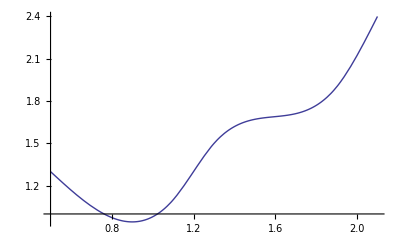

```mathematica
Plot[Piecewise[{{S0[x],0.5≤ x≤1.1},{S1[x],1.1≤ x≤1.3},{S2[x],1.3≤ x≤1.9},{S3[x],1.9≤ x≤2.1}}],{x,0.5,2.1}]
```

```mathematica
data={{0.5,1.3},{1.1,1.1},{1.3,1.5},{1.9,1.9},{2.1,2.4}}
```

{{0.5,1.3},{1.1,1.1},{1.3,1.5},{1.9,1.9},{2.1,2.4}}

```mathematica
sp = Interpolation[data, Method->"Spline"]
```

InterpolatingFunction[{{0.5,2.1}},<>]

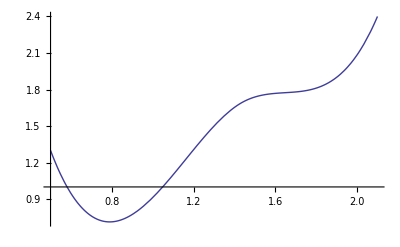

```mathematica
Plot[sp[x],{x,0.5,2.1}]
```

```mathematica
(*Problema 2:*)
x0=0.5`20
x1=0.6`20
x2=0.7`20
y0=0.4794`20 (*f(x0)*)
y1=0.5646`20(*f(x1)*)
y2=0.6443`20(*f(x2)*)
```

0.5

0.6

0.7

0.4794

0.5646

0.6443

```mathematica
(*Empezamos a mirar el punto x0. Como es un extremo del intervalo para el que tenemos datos en la tablar, solo podemos usar la fórmula de dos y de tres puntos en extremo*)
```

```mathematica
(*Exceso para x0=0.5: (f[x1]-f[x0])/(x1-x0)*)
(y1-y0)/(x1-x0)
```

0.852

```mathematica
(*Tres puntos en extremo:*)
(-3y0+4y1-y2)/(x2-x0)
```

0.8795

```mathematica
(*Para x0 no pueden usarse fórmulas de punto medio porque no hay valores tabulados de f previos a x0. De las dos aproximaciones que hemos dado, al no tener los valores de la derivada, debemos considerar que va a taner menor error absuouto a priori porque el salto de paso es de amplitud 0.1 por lo que el cuadrado es menor.*)
```

```mathematica
(*Pasamos a estudiar x1=0.6. En este caso podemos applicar las fórmulas de dos puntos regresiva, progresiva y en punto medio ya que hay valores anteriores y posteriores a x1 tabulados:*)
```

```mathematica
(*Defecto para 0.6: (f[x1]-f[x0])/(x1-x0)*)
(y1-y0)/(x1-x0)
```

0.852

```mathematica
(*Exceso para 0.6: (f[x1]-f[x2])/(x1-x2)*)
(y1-y2)/(x1-x2)
```

0.797

```mathematica
(*Punto medio para dos puntos:*)
(y2-y0)/(x2-x0)
```

0.8245

```mathematica
(*Para y1 no podemos usar la de tres puntos en extremo porque solo tenemos un punto anterior y otro posterior. La que se puede usar es la de punto medio. Observa que es formalmente la misma expresión que la de dos puntos en punto medio:*)
(y2-y0)/(x2-x0)
```

0.8245

```mathematica
(*El menor de los errores se comete a priori con el punto medio, ya que es h^2 y no con h.
Para el caso de x2=0.7, solo tenemos la fórmula de dos puntos regresiva y la de tres puntos en extremo*)
```

```mathematica
(*Defecto para 0.7: (f[x2]-f[x1])/(x2-x1)*)
(y2-y1)/(x2-x1)
```

0.797

```mathematica
(*Tres puntos en extremo:*)
(-3y2+4y1-y0)/(x0-x2)
```

0.7695

```mathematica
(*Ejercicio 3*)
```

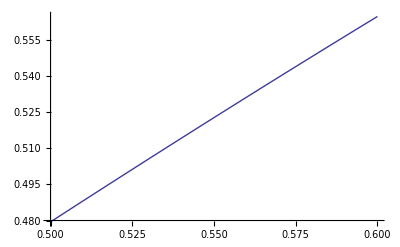

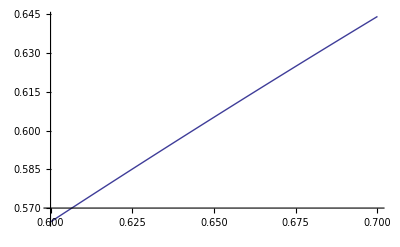

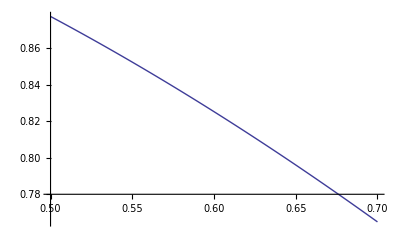

```mathematica
(*Fórmulas del error absoluto: EA=h/2*|f''|
f'' para el intervalo [0.5,0.6] y [0.6,0.7] respectivamente:*)
f[x_]:=Sin[x]
Plot[Abs[f''[x]],{x,0.5,0.6}]
Plot[Abs[f''[x]],{x,0.6,0.7}]
Plot[Abs[f'''[x]],{x,0.5,0.7}]
```

```mathematica
(*Error usando dos puntoa en extremo para el intervalo [0.5,0.6]:*)
(x1-x0)/2*Abs[f''[x1]]
(*Error usando dos puntos en extremo para el intervalo [0.6,0.7]:*)
(x2-x1)/2*Abs[f''[x2]]
(*Error usando tres puntos en extremo para el intervalo [0.5,0.7]:*)
(x2-x1)^2/3*Abs[f'''[x0]]
(*Error usando tres puntos en punto medio para el intervalo [0.5,0.7]:*)
(x2-x1)^2/6*Abs[f'''[x0]]
```

0.0282321236697517679

0.0322108843618845527

0.00292527520630124239

0.00146263760315062119

```mathematica
(*Problema 4: Usar las cotas de error para determinar el método que dé una aproximación más exacta:
Error en fórmula de dos puntos en extremo para x=3. Independientemente de ser regresiva o progresiva, la fórmula es h/2*|f''|. Como h=1 y |f''|≤3, la cota del error es:*)
1/2*3.
```

1.5

```mathematica
(*Error en fórmula de 3 puntos en punto medio para x=3. Debe tomarse con los puntos 2 y 4, por lo que h=1 y |f'''|≤6. No hay que considerar la de extremo porque la expresión es la misma pero el dividendo es 3 en lugar de 6, por lo que el resultado de la división sería mayor:*)
1^2/6. 6
```

1.

```mathematica
(*Error en fórmula de 5 puntos  en punto medio para x=3 (por mismo motivo de antes, no es necesario pensar en fórmula en extremo):*)
1^4/30*23.
```

0.766667

```mathematica
(*El error más pequeño es el de la fórmula de 5 puntos, por lo que esa debería ser la aproximación a considerar:*)
(2.4142-8*2.6734+8*3.0976-3.2804)/(12*1)
```

0.210617

```mathematica
(*Para el caso de x=3.5, no pueden considerarse ninguna de las fórmulas en extremo, pues no tenemos el valor de la imagen para x=3.5. Ahora habría que ver cuál es el error para la fórmula de tres puntos en punto medio y lo mismo para la de cinco punbtos. La amplitud h de los intervalos debería ser de 0.5, por lo tanto debería ser 2.5, 3, 3.5, 4 y 4.5. Por tanto, la de cinco puntos no es aplicable. De todos las fórmulas de que disponemos solo podemos aplicar la de tres puntos en punto medio.
ERROR:*)
0.5^2/6*6
(*APROXIMACION:*)
(3.0976-2.8974)/(4-3)
```

0.25

0.2002

```mathematica
(*Supongamos que la derivada tercera e 4:*)
1^2/6. 4
```

0.666667

```mathematica
(* En el caso de x=3, deberíamos considerar la fórmula de 3 puntos en punto medio en lugar de la de cinco puntos:*)
(3.0976-2.6734)/(4-2)
```

0.2121

```mathematica
(*Problema 6 parcial: Usar fórmula de 3 puntos en extremo para los extremos y de punto medio para ese punto:*)
x0=0.25`20
x1=0.5`20
x2=0.75`20
```

0.25

0.5

0.75

```mathematica
f[x_]:=Cos[Pi x]
(*Aproximación de f'[0.25]*)
1/(2(x1-x0))(-3*f[x0]+4 f[x1]-f[x2])
(*Aproximación de f'[0.5]:*)
1/(2(x2-x1))(f[x2]-f[x0])
(*Aproximación de f'[0.25]*)
1/(2(x1-x2))(-3*f[x2]+4 f[x1]-f[x0])
```

-2.828427124746190098

-2.828427124746190098

-2.8284271247461901

```mathematica
f'[0.25]
f'[0.5]
f'[0.75]
```

-2.22144

-3.14159

-2.22144

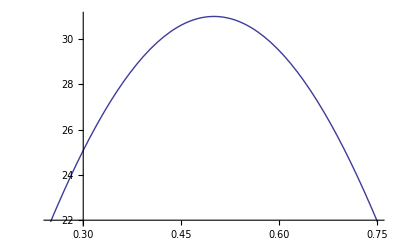

```mathematica
(*Error absoluto para las aproximaciones en 0.25 y 0.75 se hacen con intervalo [0.25,0.75] y fórmula de error h^2/2|f'''|. Dibujamos la f''' en el intervalo:*)
Plot[Abs[f'''[x]],{x,0.25,0.75}]
```

```mathematica
(* Máximo en 0.5, por tanto el error en las derivadas de los extremos es:*)
(0.25`20)^2/2 Abs[f'''[0.5]]
```

0.968946

```mathematica
(*Error absoluto para las aproximaciones en 0.25 y 0.75 se hacen con intervalo [0.25,0.75] y fórmula de error h^2/6|f'''|. *)
(0.25`20)^2/6 Abs[f'''[0.5]]
```

0.322982